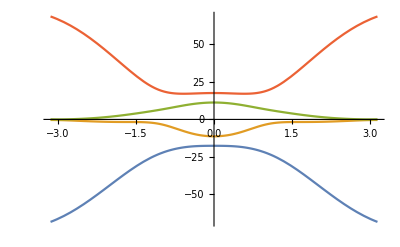

```mathematica
f1[k_,a_]:=1+Exp[ⅈ*a*k(Cos[θ]+√3 Sin[θ])]+Exp[ⅈ*a*k(Cos[θ]-√3 Sin[θ])]
f2[k_,a_]:=1+Exp[-ⅈ*a*k(Cos[θ]+√3 Sin[θ])]+Exp[-ⅈ*a*k(-Cos[θ]+√3 Sin[θ])]
f3[k_,a_]:=Exp[-ⅈ*a*k(2*√3 Sin[θ])]+Exp[-ⅈ*a*k(Cos[θ]+√3 Sin[θ])]+Exp[-ⅈ*a*k(-Cos[θ]+√3 Sin[θ])]
f4[k_,a_]:=2(Cos[a*k(Cos[θ]+√3 Sin[θ])]+Cos[a*k(-Cos[θ]+√3 Sin[θ])]+Cos[a*k(Cos[θ])])
a1=1.5312;
a2=4.6730;
a3=9.5007;
Δ=61.5978;
θ=1.08;
H[a_]:={{0,a1*f1[a,k],a2*f2[a,k],0},{a1*f1[a,-k],0,0,-a2*f3[a,k]},
{a2*f2[a,-k],0,-Δ+a3*f4[a,k],0},{0,-a2*f3[a,-k],0,Δ-a3*f4[a,k]}}
ev4=Table[Eigenvalues[Re[H[a]]][[i]],{i,1,4,1}]/.Thread[{a}->{0.5}];
Plot[ev4,{k,-π,π}]
```